## Fit student correctness to various models

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bvds/Andes2/LogProcessing/moment-of-learning

```mathematica
data["student"]=Import["guerra-summer-2011-kc-opps.csv"];
```

```mathematica
Take[data["student"],5]
```

{{accel-at-rest,asu_9Q1920841f2ca4d1fasul1_c,md5:1da7d76bc3d524d51da47dde26ee8f95,0,1},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_e,md5:e3e61859acb08ee896e06e1020f95a49,0},{accel-constant-speed,asu_9Q1920841f2ca4d1fasul1_c,md5:b50efcf571b671cf01b499841c66daf2,0},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e66c328693800f93b41f13d97b78e19b,1},{apply-net-work,asu_9Q1920841f2ca4d1fasul1_e,md5:e9747bab59caf0446778cc6a65a8ac2e,0}}

### Fitting routines

```mathematica
(* For these functions, n goes from 1 to number of steps *)
logistic[n_,{mu_,b_}]:=1/(Exp[-b  n+mu]+1); (* this choice of parameters gives finite constraint region *)
step[n_,{nl_,pg_,ps_}]:=pg+(Sign[n-nl+1/2]+1) (1-ps-pg)/2;
(* Need (n-1) so ps and pg bounds ares simple *)
bkt[n_,{b_,pg_,ps_}]:=1-ps-(1-ps-pg)*Exp[-b (n-1)];
(* For testing *)
(* I had some concern that the original method was not finding the global minimu *)
bkt2[nn_][n_,{a_,pg_,ps_}]:=1-ps-(1-ps-pg) a^((n-1)/nn);
half[n_,{}]:=1/2;
```

```mathematica
(* AIC for step model calculated explicitly. *)
stepFit[data_,i_]:=Block[{l0=Count[Take[data,i-1],0],l1=Count[Take[data,i-1],1],u0=Count[Drop[data,i-1],0],u1=Count[Drop[data,i-1],1],g,s,logLike=0},If[l0+l1>0,g=l1/(l0+l1);logLike+=If[l1>0,l1*Log[g],0]+If[l0>0,l0*Log[1-g],0]];If[u0+u1>0,s=u0/(u0+u1);logLike+=If[u0>0,u0*Log[s],0]+If[u1>0,u1*Log[1-s],0]];logLike];
stepGain[data_,i_]:=If[i==1,0,Block[{l0=Count[Take[data,i-1],0],l1=Count[Take[data,i-1],1],u0=Count[Drop[data,i-1],0],u1=Count[Drop[data,i-1],1],gain=1},If[l0+l1>0,gain-=l1/(l0+l1)];If[u0+u1>0,gain-=u0/(u0+u1)];gain]];
stepFit[data_]:=Block[{best=-Infinity,lBest},Do[Block[{logLike=stepFit[data,i]},If[logLike>best,best=logLike;lBest=i]],{i,Length[data]}];
(* Not clear if this is really 3 parameters when data is short *)If[Length[data]≥3,2*3-2*N[best]]]
```

```mathematica
(* Akaike weights for step model when all L are equally probable. *)
avgWeights[n_]:=Table[If[i==1,Exp[1],1],{i,n}]/(Exp[1]+n-1)
```

```mathematica
logger[x_?NumberQ,params_]:= (* not used now. *)Which[0<x≤1,Log[x],x==0,(* NMaximize can't handle -Infinity *)-10^50,True,Print["Invalid probability ",x," for ",params];If[x<0,-Infinity,0]]
logProb[model_,params_,data_]:=Sum[Log[If[data[[i]]==1,model[i,params],1-model[i,params]]],{i,Length[data]}]
maxer[model_,vars_,constraints_,data_]:=Which[
(* too few data points *)
Length[data]<Length[vars],Null,
(* All three functions can perfectly fit to all ones or zeros, but numerical fit is hard. *)
Count[data,0]==0 || Count[data,1]==0,2 Length[vars],True,
Block[{x=NMaximize[{logProb[model,vars,data],constraints[data]},vars,
(* If you plot the likelihood as a function of parameter, you see a space with many valleys, presumably one per data point.  Thus we make the number of starting points propotional to length of the dataset. *)Method->{"RandomSearch","SearchPoints"->Max[10 Length[vars],Length[data]],Method->"ConjugateGradient"}]},If[NumberQ[x[[1]]],2Length[vars]-2 x[[1]],Print[data,x];False]]]
```

```mathematica
logisticConstraints[x_]:=Block[{delta=15,ones=Position[x,1,1],zeros=Position[x,0,1]},mu≥Max[zeros[[-1,1]]*b,zeros[[1,1]]*b]-delta&& mu≤Min[ones[[1,1]]*b,ones[[-1,1]]*b]+delta&& b>-2 delta/Max[1,ones[[-1,1]]-zeros[[1,1]]] && b<2 delta/Max[1,zeros[[-1,1]]-ones[[1,1]]]]
```

```mathematica
bktConstraints[_]:=Block[{delta=15},pg≥Exp[-delta] && ps≥Exp[-delta] && pg≤1-Exp[-delta] && ps≤ 1-Exp[-delta] &&b≥0 && b<delta]
```

```mathematica
bkt2Constraints[x_]:=Block[{delta=15},pg≥Exp[-delta] && ps≥Exp[-delta] && pg≤1-Exp[-delta] && ps≤ 1-Exp[-delta] &&a≥Exp[-Length[x] delta] && a<1-Exp[-delta]]
```

Correction to get AIC_c

```mathematica
aicCorrection[k_,n_]:=2 k (k+1)/(n-k-1)
```

### Generate random data and table of AIC' s

Best possible data set

```mathematica
data["ideal",n_:1]:=Flatten[Table[Map[Block[{nd=Length[#]-3,nn},nn=If[nd==1,1,RandomInteger[nd-2]+1];Join[{Null,Null,Null},Table[0,{nn}],Table[1,{nd-nn}]]]&,data["student"]],{n}],1];
```

Make random data, 50 % correct

```mathematica
data["randomC",n_:100]:=Table[Join[{Null,Null,Null},Table[RandomInteger[],{n}]],{10000/n}];
```

Make random data, span space, with 50 % correct

```mathematica
data["even",n_]:=Table[Join[{Null,Null,Null},IntegerDigits[i-1,2,n]],{i,2^n}];
```

```mathematica
data["random",n_:1]:=Flatten[Table[Map[Join[{Null,Null,Null},Table[RandomInteger[],{Length[Drop[#,3]]}]]&,data["student"]],{n}],1];
```

```mathematica
data["reorder",n_:1]:=Flatten[Table[Map[Join[{Null,Null,Null},RandomSample[Drop[#,3]]]&,data["student"]],{n}],1];
```

Make exponential data

```mathematica
data["exponential"]=Table[Join[{Null,Null,Null},Block[{a=Random[],b=Random[],c=Random[],n=100},Table[If[Random[]<a+(b-a) c^( i/n),1,0],{i,n}]]],{100}];
```

```mathematica
ColumnForm[Transpose[{data["student"],data["ideal"]}]]
```

### Generate full tables of AIC' s

```mathematica
generateAICs[set__]:=Map[{#[[1]],#[[3]],Length[Drop[#,3]],Print[#[[1]]," logistic ",#[[3]]];maxer[logistic,{mu,b},logisticConstraints,Drop[#,3]],stepFit[Drop[#,3]],Print[#[[1]]," bkt ",#[[3]]];maxer[bkt,{b,pg,ps},bktConstraints,Drop[#,3]],maxer[bkt2[Length[Drop[#,3]]],{a,pg,ps},bkt2Constraints,Drop[#,3]],-2*N[logProb[half,{},Drop[#,3]]]}&,data[set]]
```

This takes a long time to calculate.  Do as batch process; see file "generate-fits.m"

```mathematica
allValues=generateAICs["student"];
```

```mathematica
Save["fitAll.m",allValues]
```

```mathematica
randomValues100=generateAICs["random",100];
```

```mathematica
Save["fitRandomData100.m",randomValues100]
```

```mathematica
Length[data["random",10]]
```

3

```mathematica
randomValues10=generateAICs["random",10];
```

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

Null logistic Null

Null bkt Null

```mathematica
Save["fitRandomData10.m",randomValues10]
```

### Step function model: Plot Akaike weights.

#### Distribution of weighted gains

```mathematica
Clear[weightedGains];weightedGains[set__]:=weightedGains[set]=Map[Function[{x,y},x/Apply[Plus,x] y][Table[Block[{aic=2*If[i==1,1,2]-2.*stepFit[Drop[#,3],i]},Exp[-aic/2]],{i,Length[Drop[#,3]]}],Table[stepGain[Drop[#,3],i],{i,Length[Drop[#,3]]}]]&,data[set]];
```

Numerically estimate standard deviation of weighted gain for reorder dataset where dataset has same number of sequences as student dataset.  Note the result is exactly the same as when the standard deviation of the mean is used.

```mathematica
StandardDeviation[Table[Block[{xx=weightedGains["reorder",1]},weightedGains["reorder",1]=.;Total[Flatten[xx]]/Length[xx]],{10}]]
```

0.0077422

```mathematica
%/Sqrt[10]
```

0.0024483

```mathematica
StandardDeviation[Table[Block[{xx=weightedGains["random",1]},weightedGains["random",1]=.;Total[Flatten[xx]]/Length[xx]],{10}]]
```

0.00495394

```mathematica
%/Sqrt[10]
```

0.00156657

In this case, however, we get an order of magnitude larger result from the standard deviation of the mean.

```mathematica
StandardDeviation[Table[Block[{xx=weightedGains["ideal",1]},weightedGains["ideal",1]=.;Total[Flatten[xx]]/Length[xx]],{10}]]
```

0.000901295

```mathematica
%/Sqrt[10]
```

0.000285015

```mathematica
gStats[set__]:=Block[{xx=weightedGains[set],xxx},
xxx=Flatten[xx];{Length[xx],Length[xxx],StandardDeviation[xxx],Total[xxx]/Length[xx],StandardDeviation[xxx] Sqrt[Length[xxx]]/Length[xx]}]
```

```mathematica
gStats["student"]
```

{2017,32030,0.0730042,0.0466674,0.00647769}

```mathematica
gStats["reorder",10]
```

{20170,320300,0.0713389,-0.00172275,0.0020017}

```mathematica
gStats["random",10]
```

{20170,320300,0.078627,0.00133552,0.0022062}

```mathematica
gStats["ideal",10]
```

{20170,320300,0.139267,0.524222,0.00390769}

```mathematica
gStats2[set__]:=Block[{xx=weightedGains[set],xxx,n},
xxx=Flatten[xx];n=Length[xx];{Length[xxx],n,N[Total[Select[xxx,#>1/2&]]/n],N[Total[Select[xxx,#<-1/2&]]/n],N[Total[Select[xxx,#>1/20&]]/n],N[Total[Select[xxx,#<-1/20&]]/n]}]
```

```mathematica
gStats2["student"]
```

{32030,2017,0.0777815,-0.0402763,0.118149,-0.0733867}

```mathematica
gStats2["reorder",10]
```

{320300,20170,0.0547603,-0.0572539,0.0908107,-0.0936874}

```mathematica
gStats2["random",10]
```

{320300,20170,0.0676128,-0.0672031,0.115425,-0.114403}

```mathematica
gStats2["ideal",10]
```

{320300,20170,0.466094,0.,0.506149,0.}

Numbers used in paper for student dataset.  Should match bins in weighed gains histogram.

```mathematica
gStats3[set__]:=Block[{xx=weightedGains[set],xxx,n},
xxx=Flatten[xx];n=Length[xx];{Length[xxx],n,Length[Select[xxx,#>1/2&]],Length[Select[xxx,#<-1/2&]],Length[Select[xxx,#>1/39&]],Length[Select[xxx,#<-1/39&]],Length[Select[xxx,Abs[#]<1/39&]]}]
```

```mathematica
gStats3["student"]
```

{32030,2017,257,133,1312,988,29730}

```mathematica
Clear[histline];histLine[set__]:=histLine[set]=Block[{xxx=Flatten[weightedGains[set]],dx=2/39},Flatten[Table[{{i-dx/2,#},{i+dx/2,#}}&[Max[0.001,Length[Select[xxx,i-dx/2≤#<i+dx/2&]]]],{i,-1+dx/2,1-dx/2,dx}],1]];
```

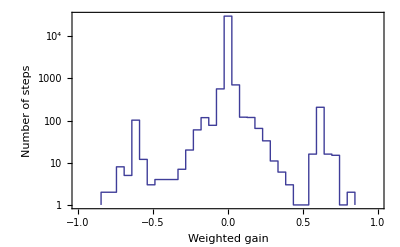

```mathematica
wgh=ListLogPlot[histLine["student"],Joined->True,Axes->False,Frame->True,FrameLabel->{"Weighted gain","Number of steps"},BaseStyle->{FontSize->12},PlotRange->{{-1,1},{1,All}}]
```

```mathematica
Export["weighted-gain-histogram.eps",wgh]
```

weighted-gain-histogram.eps

If I blow it up, I get the same shape!

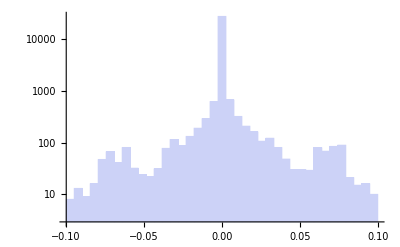

```mathematica
Histogram[Flatten[weightedGains["student"]],{-0.1,0.1,0.2/39},"LogCount"]
```

```mathematica
Needs["PlotLegends`"]
```

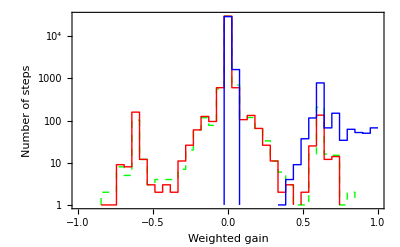

```mathematica
wgh2=ListLogPlot[{histLine["student"],histLine["reorder",1],histLine["ideal",1]},Joined->True,Axes->False,Frame->True,FrameLabel->{"Weighted gain","Number of steps"},LegendShadow->False,

PlotStyle->{{Dashed,Green},Red,Blue},LegendSize->{0.6,.25},LegendTextSpace->4,PlotLegend->{"student dataset","random dataset","ideal dataset"},
LegendPosition->{0.23,.32},BaseStyle->{FontSize->12},PlotRange->{{-1,1},{1,All}}]
```

```mathematica
Export["weighted-gain-histogram2.eps",wgh2]
```

weighted-gain-histogram2.eps

Partial sum of weighed gains, adding all weighed gains whose magnitude is less than the cutoff.  This shows that most of the sum is from the weighed gains > 0.5.

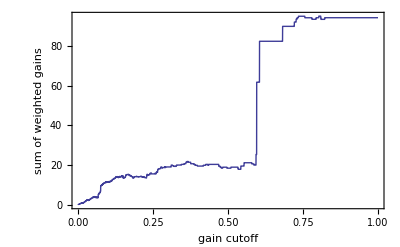

```mathematica
Block[{xxx=Flatten[weightedGains["student"]]},Plot[Total[Select[xxx,Abs[#]<x&]],{x,0,1},Axes->False,Frame->True,FrameLabel->{"gain cutoff","sum of weighted gains"},BaseStyle->{FontSize->12}]]
```

Partial sum of positive/negative weighed gains, adding all positive/negative weighed gains whose magnitude is less than the cutoff.  This shows that most of the positive/negative asymmetry is from large gains.

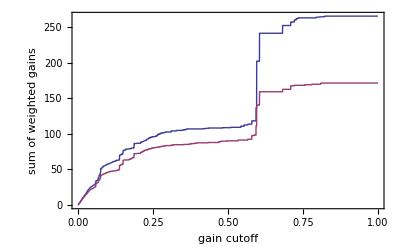

```mathematica
Block[{xxx=Flatten[weightedGains["student"]]},Plot[{Total[Select[xxx,0<#<x&]],Abs[Total[Select[xxx,0>#>-x&]]]},{x,0,1},Axes->False,Frame->True,FrameLabel->{"gain cutoff","sum of weighted gains"},BaseStyle->{FontSize->12}]]
```

#### Histogram of lengths for paper

```mathematica
histLineStudent=Block[{xxx=Map[Log[Length[Drop[#,3]]]&,data["student"]],max,dx},
max=Max[xxx];
dx=max/20;Flatten[Table[{{Exp[i-dx/2],#},{Exp[i+dx/2],#}}&[Max[0.001,Length[Select[xxx,i-dx/2≤#<i+dx/2&]]]],{i,0,max,dx}],1]];
```

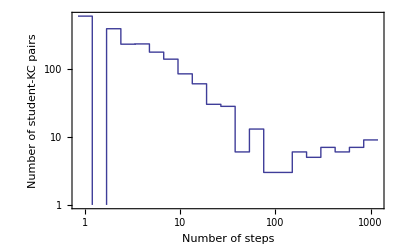

```mathematica
sklh=ListLogLogPlot[histLineStudent,Joined->True,PlotRange->{1,All},Axes->False,Frame->True,FrameLabel->{"Number of steps","Number of student-KC pairs"},BaseStyle->{FontSize->12}]
```

```mathematica
Export["student-kc-length-histogram.eps",sklh]
```

student-kc-length-histogram.eps

#### Example KC for paper

```mathematica
data1={1,0,0,1,1,1,0,1,0,1};
```

```mathematica
data1={0,0,0,1,1,0,1,1};
```

```mathematica
aics=Table[{i,N[2*If[i==1,1,2]-2*stepFit[data1,i-1]]},{i,Length[data1]}]
```

{{1,13.0904},{2,13.5607},{3,11.6382},{4,9.00402},{5,12.9974},{6,14.5492},{7,11.6382},{8,13.5607}}

```mathematica
weights1=Function[x,x/Apply[Plus,x]][N[Table[Block[{aic=2*If[i==1,1,2]-2*stepFit[data1,i-1]},Exp[-aic/2]],{i,Length[data1]}]]]
```

{0.0626582,0.0495269,0.129514,0.483407,0.0656404,0.030213,0.129514,0.0495269}

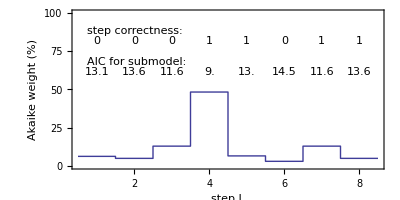

```mathematica
stepWeightsPlot=Block[{n=Length[data1],yt=85,y2=65},ListPlot[Flatten[Table[{{i-1/2,#},{i+1/2,#}}&[weights1[[i]]*100],{i,n}],1],Epilog->{Text["step correctness:",{0.75,yt},{-1,-1}],Table[Text[data1[[i]],{i,yt},{0,1}],{i,n}],
Text["AIC for submodel:",{0.75,y2},{-1,-1}],
	Map[Text[Round[#[[2]],0.1],{#[[1]],y2},{0,1}]&,aics]},PlotRange->{{1/2,n+1/2},{0,100}},
Joined->True,
FrameLabel->{"step L","Akaike weight (%)"},BaseStyle->{FontSize->12}, AspectRatio->1/2,Axes->False,Frame->True]]
```

```mathematica
Export["step-weights.eps",stepWeightsPlot]
```

step-weights.eps

### Stuff

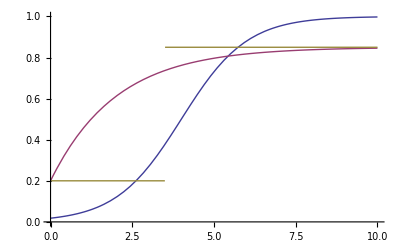

```mathematica
Plot[{logistic[x,{4,1}],bkt[x,{.5,.2,.15}],step[x,{4,.2,.15}]},{x,0,10},PlotRange->{0,1}]
```

### Analyze

Logistic, step model, Baysian Knowledge Tracing

```mathematica
Get["fitAll.m"];
```

```mathematica
Get["fitRandomData100.m"];
```

```mathematica
Get["fitRandomData10.m"];
```

Here, set cutValues to the desired variable to get a particular dataset.

```mathematica
cutValues[ss_]:=Select[ss,#[[3]]≥10&]
```

```mathematica
distinctCounts[ss_]:={Length[cutValues[ss]],Length[Union[Map[First,cutValues[ss]]]],Length[Union[Map[#[[2]]&,cutValues[ss]]]]}
```

```mathematica
aics[ss_]:=Map[{#[[4]]+aicCorrection[2,#[[3]]],#[[5]]+aicCorrection[3,#[[3]]],Min[#[[6]],#[[7]]]+aicCorrection[3,#[[3]]]}&,cutValues[ss]];
```

```mathematica
akaikeWeights[ss_]:=Map[Block[{y=Exp[-#/2]},y/Apply[Plus,y]]&,aics[ss]];
```

```mathematica
akaikeRawWeights[ss_]:=Map[Block[{y=Exp[-#/2]},y/Apply[Plus,y]]&,Map[Drop[#,3]&,allValues[ss]]]
```

```mathematica
weightAverages[ss_]:=Map[{Median[#],Mean[#],StandardDeviation[#]/Length[#]}&,Transpose[akaikeWeights[ss]]]
```

random generated data length 100

```mathematica
weightAverages[randomValues100]
```

{{0.264659,0.254179,0.00113399},{0.549613,0.567605,0.00155237},{0.18248,0.178216,0.000658681}}

random generated data length 10

```mathematica
weightAverages[randomValues10]
```

{{0.630311,0.618333,0.00010735},{0.238083,0.263275,0.000105761},{0.114574,0.118392,0.0000475398}}

real data

```mathematica
weightAverages[allValues]
```

{{0.527527,0.49128,0.000687798},{0.329957,0.365027,0.00067914},{0.135349,0.143693,0.000259762}}

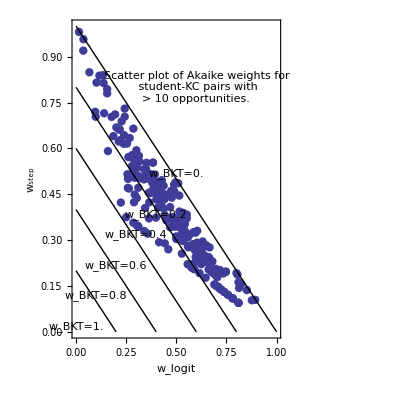

```mathematica
scatterWeights=ListPlot[Map[Take[#,2]&,akaikeWeights[allValues]],AspectRatio->1,PlotStyle->{PointSize[0.015]},Epilog->{Text[Style["Scatter plot of Akaike weights for\n student-KC pairs with\n> 10 opportunities.",TextAlignment->Right],{.6,0.8}],Table[{Line[{{0,i},{i,0}}],Text[SequenceForm[Subscript[w,BKT],"=",N[1-i]],{i/2,i/2},{0,If[i==4/5,1,-1]},{1,-1}]},{i,0,1,1/5}]},PlotRange->{{0,1},{0,1}},Axes->False,Frame->True,FrameLabel->{Subscript[w,logit],Subscript[w,step]},BaseStyle->{FontSize->12}]
```

```mathematica
Export["scatter-weights.eps",scatterWeights]
```

scatter-weights.eps

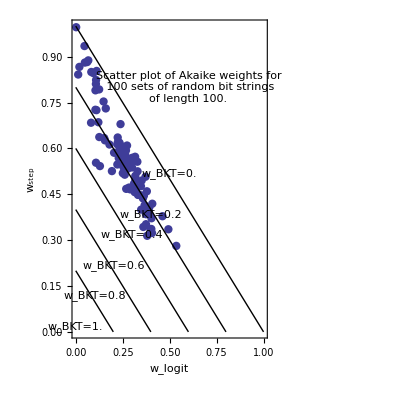

```mathematica
scatterRandomWeights=ListPlot[Map[Take[#,2]&,akaikeWeights[randomValues100]],AspectRatio->1,PlotStyle->{PointSize[0.015]},Epilog->{Text[Style["Scatter plot of Akaike weights for\n 100 sets of random bit strings\nof length 100.",TextAlignment->Right],{.6,0.8}],Table[{Line[{{0,i},{i,0}}],Text[SequenceForm[Subscript[w,BKT],"=",N[1-i]],{i/2,i/2},{0,If[i==4/5,1,-1]},{1,-1}]},{i,0,1,1/5}]},PlotRange->{{0,1},{0,1}},Axes->False,Frame->True,FrameLabel->{Subscript[w,logit],Subscript[w,step]},BaseStyle->{FontSize->12}]
```

```mathematica
Export["scatter-random-weights.eps",scatterRandomWeights]
```

scatter-random-weights.eps

```mathematica
Histogram3D[Map[Take[#,2]&,akaikeWeights[randomValues10]],{{0,1,0.02},{0,1,0.02}},PlotRange->{{0,1},{0,1},All}]
```

-Graphics3D-